# Document Image Binarization Using System of Nonlinear PDEs

## u_t=D_u∇^2 u+S_u u(1-u)(u-v) v_t=D_v∇^2 v-S_v v(1-v)(v-τ)

## Numerical Code

```mathematica
andGo[Du_,Su_,Dv_,Sv_,τ_,u0in_,v0in_]:=(
u0=u0in;
v0=v0in;
(*
img=1-ImageData[ColorConvert[img,"Grayscale"]];
{n,m}=Dimensions[img];
(*img=img[[1;;Min[{n,m}],1;;Min[{n,m}]]];
{n,m}=Dimensions[img];*)

img=ImageData[ImageAdjust[Image[img]]];
averagingKernel[r1_,r2_]:=1/((2r1+1)(2r2+1))BoxMatrix[{r1,r2}];
Δimg=ImageData[ImageConvolve[Image[img],GaussianMatrix[{7,7}]]];
(*Δimg=ImageData[ImageConvolve[Image[img],averagingKernel[7,7]]];*)
(*v0=ImageData[ImageAdjust[Image[Δimg]]];*)
(*v0=ImageData[ImageAdjust[Image[img-Δimg]]];*)
(*v0=Δimg;*)
(*v0=ImageData[ImageAdjust[Image[img/Δimg]]];*)
v0//ArrayPlot;


u0=img+0*RandomReal[{0,0.1},{n,m}];
u0=ImageData[ImageAdjust[Image[img-Δimg]]];
v0=ImageData[ImageConvolve[Image[u0],GaussianMatrix[{7,7}]]];
*)
{n,m}=Dimensions[u0];
finalk=200;

dx=1/(n-1);
dy=1/(m-1);
(*
a[t_]:=Tanh[3 10^3(t)];
a[t_]:=1/2+1/2 Sin[(2π)/(finalk dt)t]
a[t_]:=Exp[(-2t)/(finalk dt)]
a[t_]:=Exp[t/(1.5 finalk dt)]-1
*)
dt=0.1dx dy;
(*cd=2*0.005;
cs=1/dt 0.05;
ca=0.0005;
*)
A=SparseArray[{{i_,i_}->-2.,{i_,j_}/;Abs[i-j]==1->1.},{n,n},0.];
A[[1,2]]=2;
A[[-1,-2]]=2;

B=SparseArray[{{i_,i_}->-2.,{i_,j_}/;Abs[i-j]==1->1.},{m,m},0.];
B[[1,2]]=2;
B[[-1,-2]]=2;
B=Transpose[B];

u1=2u0;
v1=2v0;
nrmchange={};
count=0;

Monitor[
k=1;
(*For[k=1,k≤finalk,k++,*)
While[Norm[u1-u0](*Norm[v1-v0]*)>10^-1&&count<40,
count++;
u1=u0;
v1=v0;
u0=u0+dt/dx^2 Du(A.u0)+dt/dy^2 Du(u0.B)+dt Su u0(1-u0)(u0-v0);
v0=v0+dt/dx^2 Dv(A.v0)+dt/dy^2 Dv(v0.B)-dt Sv v0(1-v0)(v0-(*Mean[Mean[a0]]*)τ);
(*cd=cd(1+Tanh[(k dt)/1000]);
cs=cs(1-Tanh[(k dt)/1000]);*)
k++;
nrmchange=Join[nrmchange,{Norm[u1-u0]}];
],
{
ArrayPlot[u0,ImageSize->400],
ArrayPlot[v0,ImageSize->400],
(*ArrayPlot[ImageData[Binarize[Image[u0]]],ImageSize->400],
ArrayPlot[Positive[u0-a0]/.{False->0,True->1},ImageSize->400],
Plot[x(x-1)(x-1+Mean[Mean[a0]]),{x,0,1}],*)
Norm[u1-u0],Norm[v1-v0](*,k,ListLinePlot[nrmchange]*)}];

gt=Import[gtfn];
gt=1-ImageData[ColorConvert[gt,"Grayscale"]];

res=Positive[u0-v0]/.{False->0,True->1};
res=ImageData[Binarize[Image[res]]];
res2=u0;
res2=ImageData[Binarize[Image[res2]]];

Image[gt-res];
Image[res];
Image[res2];
Return[Norm[ImageData[Binarize[Image[gt]]]-ImageData[Binarize[Image[res]]],1]]
(*Norm[gt-res2,1]/(n*m)*)
)
(*{
ArrayPlot[u0,ImageSize->400],
ArrayPlot[img,ImageSize->400],
ArrayPlot[ImageData[Binarize[Image[u0]]],ImageSize->400],
ArrayPlot[Positive[u0-a0]/.{False->0,True->1},ImageSize->400]
(*,Norm[u1-u0],k,ListLinePlot[nrmchange]*)};*)

andGoFMSurface[Du_,Su_,Dv_,Sv_,τ_,pic_]:=(
imgfn=NotebookDirectory[]<>"\\Document Images\\"<>pic<>(*".png"*)".jpg";
gtfn=NotebookDirectory[]<>"\\Document Images\\"<>pic<>(*"GT.png"*)"GT.jpg";

(*img=Image[ImageData[Import[imgfn]]];*)
img=Image[ImageData[Import[imgfn]][[1;;-13,1;;-13]]];

count=0;

img=1-ImageData[ColorConvert[img,"Grayscale"]];
img=ImageData[ImageAdjust[Image[img]]];
averagingKernel[r1_,r2_]:=1/((2r1+1)(2r2+1))BoxMatrix[{r1,r2}];
Δimg=ImageData[ImageConvolve[Image[img],GaussianMatrix[{7,7}]]];
(*Δimg=ImageData[ImageConvolve[Image[img],averagingKernel[7,7]]];*)
(*v0=ImageData[ImageAdjust[Image[Δimg]]];*)
(*v0=ImageData[ImageAdjust[Image[img-Δimg]]];*)
(*v0=Δimg;*)
(*v0=ImageData[ImageAdjust[Image[img/Δimg]]];*)

(*u0=img;
v0=Δimg;*)

u0=ImageData[ImageAdjust[Image[img-Δimg]]];
v0=ImageData[ImageConvolve[Image[u0],GaussianMatrix[{7,7}]]];


{n,m}=Dimensions[u0];

finalk=200;

dx=1/(n-1);
dy=1/(m-1);
dt=0.1dx dy;

A=SparseArray[{{i_,i_}->-2.,{i_,j_}/;Abs[i-j]==1->1.},{n,n},0.];
A[[1,2]]=2;
A[[-1,-2]]=2;

B=SparseArray[{{i_,i_}->-2.,{i_,j_}/;Abs[i-j]==1->1.},{m,m},0.];
B[[1,2]]=2;
B[[-1,-2]]=2;
B=Transpose[B];

u1=2u0;
v1=2v0;
nrmchange={};

Monitor[
k=1;
While[Norm[u1-u0](*Norm[v1-v0]*)>0.1&&count<40,
count++;
u1=u0;
v1=v0;
u0=u0+dt/dx^2 Du(A.u0)+dt/dy^2 Du(u0.B)+dt Su u0(1-u0)(u0-v0);
v0=v0+dt/dx^2 Dv(A.v0)+dt/dy^2 Dv(v0.B)-dt Sv v0(1-v0)(v0-τ);
k++;
nrmchange=Join[nrmchange,{Norm[u1-u0]}];
],
{
ArrayPlot[u0,ImageSize->400],
ArrayPlot[v0,ImageSize->400],
Norm[u1-u0],Norm[v1-v0],count
}];

gt=Import[gtfn];
gt=1-ImageData[ColorConvert[gt,"Grayscale"]];

res=Positive[u0-v0]/.{False->0,True->1};
res=ImageData[Binarize[Image[res]]];
res2=u0;
res2=ImageData[Binarize[Image[res2]]];

Module[{img=Round[res],gtt=Round[gt]},
tp=Table[img[[i,j]]==1&&img[[i,j]]==gtt[[i,j]],{i,1,n},{j,1,m}];
fp=Table[img[[i,j]]==1&&img[[i,j]]≠gtt[[i,j]],{i,1,n},{j,1,m}];
fn=Table[img[[i,j]]==0&&img[[i,j]]≠gtt[[i,j]],{i,1,n},{j,1,m}];
fn=Total[Total[fn/.{True->1,False->0}]];
tp=Total[Total[tp/.{True->1,False->0}]];
fp=Total[Total[fp/.{True->1,False->0}]];
precision=tp/(tp+fp);
recall=tp/(tp+fn);
];
(*precision//N
recall//N*)
(*Return[Norm[ImageData[Binarize[Image[gt]]]-ImageData[Binarize[Image[res]]],1]]*)
Return[(2.precision*recall)/(precision+recall)]
)
```

# Ex 1

```mathematica
pic="1984";
imgfn=NotebookDirectory[]<>"\\Document Images\\"<>pic<>".jpg";
gtfn=NotebookDirectory[]<>"\\Document Images\\"<>pic<>"GT.jpg";


img=Image[ImageData[Import[imgfn]]];

count=0;
Du=2^0*0.005;
Dv=2^0*0.005;
Su=2^0/dt 1.36;
Sv=4Su;
τ=0.55;

img=1-ImageData[ColorConvert[img,"Grayscale"]];
img=ImageData[ImageAdjust[Image[img]]];
averagingKernel[r1_,r2_]:=1/((2r1+1)(2r2+1))BoxMatrix[{r1,r2}];
Δimg=ImageData[ImageConvolve[Image[img],GaussianMatrix[{7,7}]]];
(*Δimg=ImageData[ImageConvolve[Image[img],averagingKernel[7,7]]];*)
(*v0=ImageData[ImageAdjust[Image[Δimg]]];*)
(*v0=ImageData[ImageAdjust[Image[img-Δimg]]];*)
(*v0=Δimg;*)
(*v0=ImageData[ImageAdjust[Image[img/Δimg]]];*)

u0=img;
(*u0=ImageData[ImageAdjust[Image[img-Δimg]]];
v0=ImageData[ImageConvolve[Image[u0],GaussianMatrix[{7,7}]]];*)
v0=Δimg;

rad=25;
v0=ImageData[ImageConvolve[Image[img],1/Apply[Times,Dimensions[BoxMatrix[rad]]] BoxMatrix[rad]]];
Image[1-v0];
AbsoluteTiming[test1=andGo[Du,Su,Dv,Sv,τ,u0,v0]]
ArrayPlot[Abs[Round[gt]-Round[res]]]
ArrayPlot[Round[res]]
```

{2.43662,11}

-Graphics-

-Graphics-

```mathematica
Image[1-res]
```

-Graphics-

```mathematica
Export["C:\\Users\\Byron\\Documents\\2017\\Research\\Nonlinear System for Image Binarization\\v1\\Ex1FN.eps",Image[1-res]];
```

## Compute Performance Scores

```mathematica
Module[{img=Round[res],gtt=Round[gt]},
tp=Table[img[[i,j]]==1&&img[[i,j]]==gtt[[i,j]],{i,1,n},{j,1,m}];
fp=Table[img[[i,j]]==1&&img[[i,j]]≠gtt[[i,j]],{i,1,n},{j,1,m}];
fn=Table[img[[i,j]]==0&&img[[i,j]]≠gtt[[i,j]],{i,1,n},{j,1,m}];
fn=Total[Total[fn/.{True->1,False->0}]];
tp=Total[Total[tp/.{True->1,False->0}]];
fp=Total[Total[fp/.{True->1,False->0}]];
precision=tp/(tp+fp);
recall=tp/(tp+fn);
]
precision//N
recall//N
(2.precision*recall)/(precision+recall)//N
```

0.992118

0.951098

0.971175

```mathematica
1-Total[Total[Abs[Round[res]-Round[gt]]]]/N[n*m]
```

0.991118

## F Measure Surfaces

```mathematica
inc=0.01;
DuMin=0.00;
DuMax=0.01;
SuMin=1.32;
SuMax=1.42;

inc=0.01;
DuMin=0.08;
DuMax=0.1;
SuMin=1.32;
SuMax=1.42;

inc=0.1;
DuMin=0.00;
DuMax=0.5;
SuMin=0.9;
SuMax=1.4;

τ=0.55;
```

```mathematica
FMeasureSurface1Coords=Table[{Du,Su},{Du,DuMin,DuMax,inc},{Su,SuMin,SuMax,inc}];
(*FMeasureSurface1=Table[andGoFMSurface[2^0*0.001,Su/dt,(2^0*0.001)/4,(4 Su)/dt,Du,"1984"],{Du,DuMin,DuMax,inc},{Su,SuMin,SuMax,inc}];*)
FMeasureSurface1=Table[(*Print[ToString[Du]];*)andGoFMSurface[Du,Su/dt,Du/4,(4 Su)/dt,τ,"1984"],{Du,DuMin,DuMax,inc},{Su,SuMin,SuMax,inc}];
```

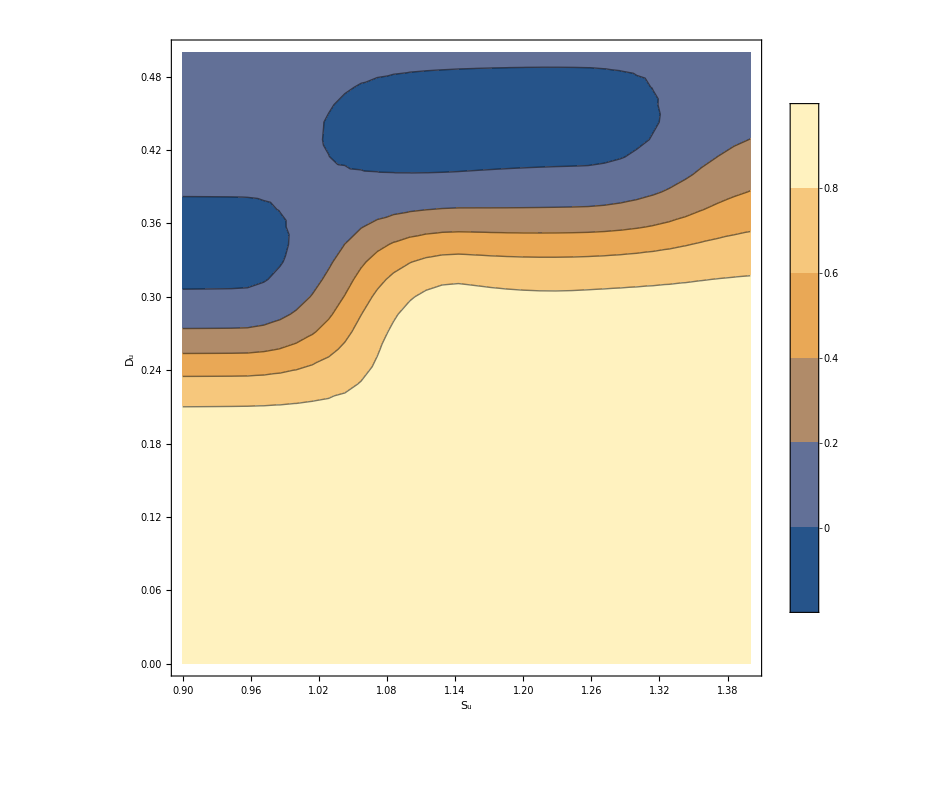

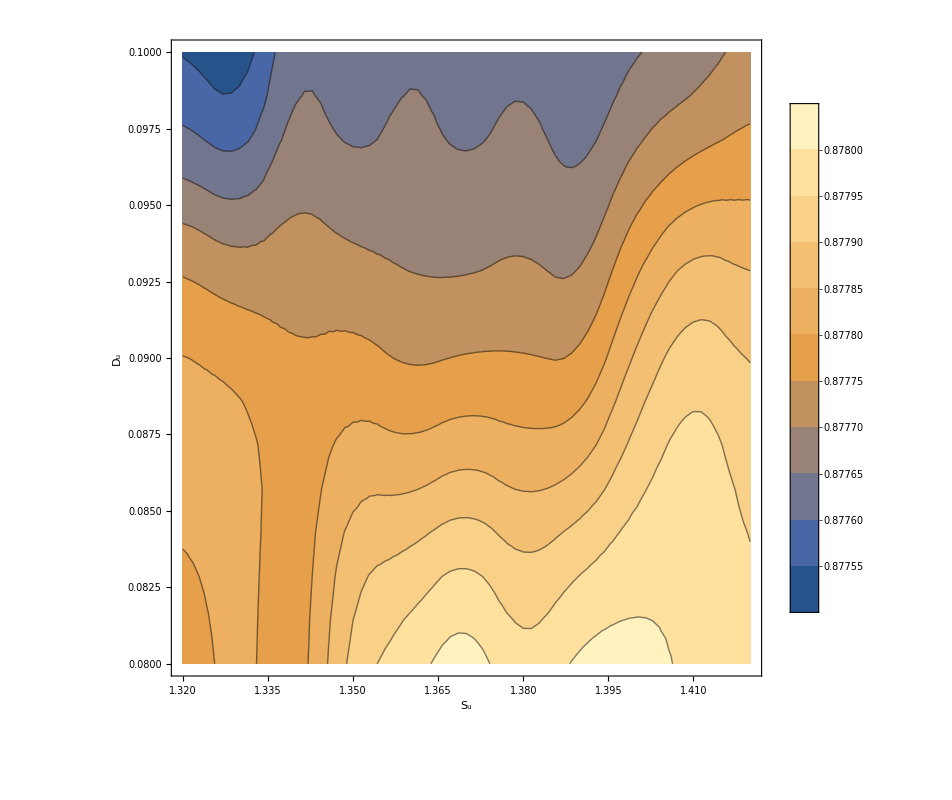

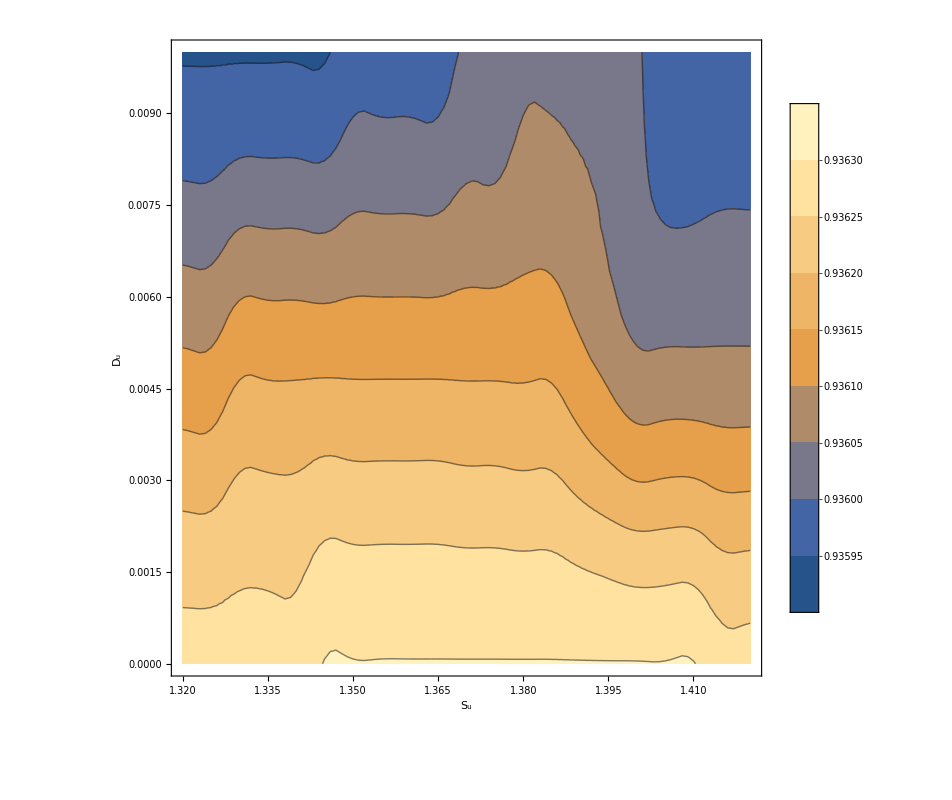

```mathematica
ListContourPlot[FMeasureSurface1,
DataRange->{{SuMin,SuMax},{DuMin,DuMax}},
InterpolationOrder->2,
ImageSize->800,
PlotLegends->Automatic,
ContourLabels->None,
Frame->True,
FrameLabel->{"S_u","D_u"},
LabelStyle->Directive[Bold, 20]]
```

```mathematica
0.93615
```

```mathematica
Export["C:\\Users\\Byron\\Documents\\2017\\Research\\Nonlinear System for Image Binarization\\v1\\Ex1FMSurface.eps",Out[141]];
```

# Ex 2

```mathematica
pic="Poem";
imgfn=NotebookDirectory[]<>"\\Document Images\\"<>pic<>".jpg";
gtfn=NotebookDirectory[]<>"\\Document Images\\"<>pic<>"GT.jpg";


img=Image[ImageData[Import[imgfn]]];
img//ImageDimensions;
img;
count=0;
Du=2^0*0.001;
Dv=Du/4;
Su=2^0/dt 1.85;
Sv=4Su;
τ=0.505;

img=1-ImageData[ColorConvert[img,"Grayscale"]];
img=ImageData[ImageAdjust[Image[img]]];
averagingKernel[r1_,r2_]:=1/((2r1+1)(2r2+1))BoxMatrix[{r1,r2}];
Δimg=ImageData[ImageConvolve[Image[img],GaussianMatrix[{7,7}]]];
(*Δimg=ImageData[ImageConvolve[Image[img],averagingKernel[7,7]]];*)
(*v0=ImageData[ImageAdjust[Image[Δimg]]];*)
(*v0=ImageData[ImageAdjust[Image[img-Δimg]]];*)
(*v0=Δimg;*)
(*v0=ImageData[ImageAdjust[Image[img/Δimg]]];*)

u0=ImageData[ImageAdjust[Image[img-Δimg]]];
(*v0=ImageData[ImageConvolve[Image[u0],GaussianMatrix[{7,7}]]];*)
rad=105;
v0=ImageData[ImageConvolve[Image[u0],1/Apply[Times,Dimensions[BoxMatrix[rad]]] BoxMatrix[rad]]];

AbsoluteTiming[test1=andGo[Du,Su,Dv,Sv,τ,u0,v0]]
```

{3.05318,18}

```mathematica
ArrayPlot[Abs[Round[gt]-Round[res]]]
ArrayPlot[Round[res]]
```

-Graphics-

-Graphics-

```mathematica
Image[1-res]
```

-Graphics-

```mathematica
Export["C:\\Users\\Byron\\Documents\\2017\\Research\\Nonlinear System for Image Binarization\\v1\\Ex2FN.eps",Image[1-res]];
```

## Compute Performance Scores

```mathematica
Module[{img=Round[res],gtt=Round[gt]},
tp=Table[img[[i,j]]==1&&img[[i,j]]==gtt[[i,j]],{i,1,n},{j,1,m}];
fp=Table[img[[i,j]]==1&&img[[i,j]]≠gtt[[i,j]],{i,1,n},{j,1,m}];
fn=Table[img[[i,j]]==0&&img[[i,j]]≠gtt[[i,j]],{i,1,n},{j,1,m}];
fn=Total[Total[fn/.{True->1,False->0}]];
tp=Total[Total[tp/.{True->1,False->0}]];
fp=Total[Total[fp/.{True->1,False->0}]];
precision=tp/(tp+fp);
recall=tp/(tp+fn);
]
precision//N
recall//N
(2.precision*recall)/(precision+recall)//N
1-Total[Total[Abs[Round[res]-Round[gt]]]]/N[n*m]
```

0.928618

0.944106

0.936298

0.985421

0.926107

0.944809

0.935365

0.985182

0.926191

0.944497

0.935254

0.98516

```mathematica
inc=0.005;
DuMin=0.0;
DuMax=0.01;

inc=0.1;
DuMin=0.0;
DuMax=0.1;
SuMin=1.2;
SuMax=1.9;
τ=0.45;
```

```mathematica
FMeasureSurface2Coords=Table[{Du,Su},{Du,DuMin,DuMax,inc},{Su,SuMin,SuMax,inc}];
FMeasureSurface2=Table[andGoFMSurface[Du,Su/dt,Du/4,(4 Su)/dt,τ,"Poem"],{Du,DuMin,DuMax,inc},{Su,SuMin,SuMax,inc}];
(*FMeasureSurface2=Table[andGoFMSurface[2^0*0.004,Su/dt,(2^0*0.001)/4,(4 Su)/dt,Du,"Poem"],{Du,DuMin,DuMax,inc},{Su,SuMin,SuMax,inc}];*)
```

```mathematica
FMeasureSurface2//MatrixForm
```

(0.935483 | 0.935486 | 0.935486 | 0.935486 | 0.935506 | 0.935486 | 0.935486 | 0.935483
0.928037 | 0.92868 | 0.929326 | 0.929941 | 0.930428 | 0.93076 | 0.931084 | 0.931299)

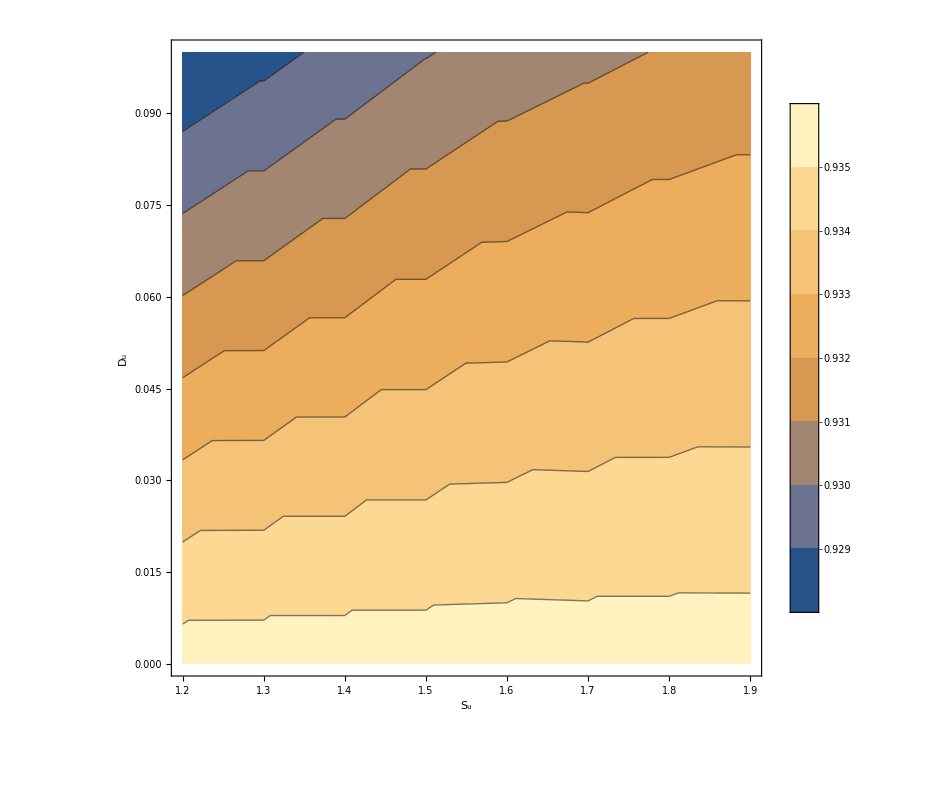

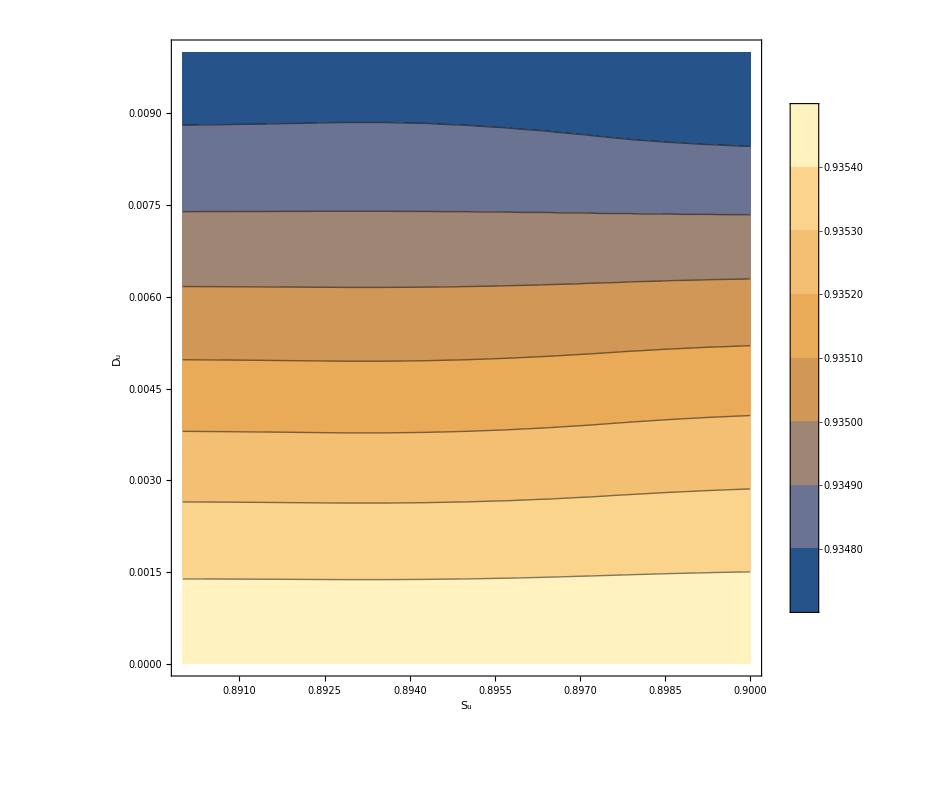

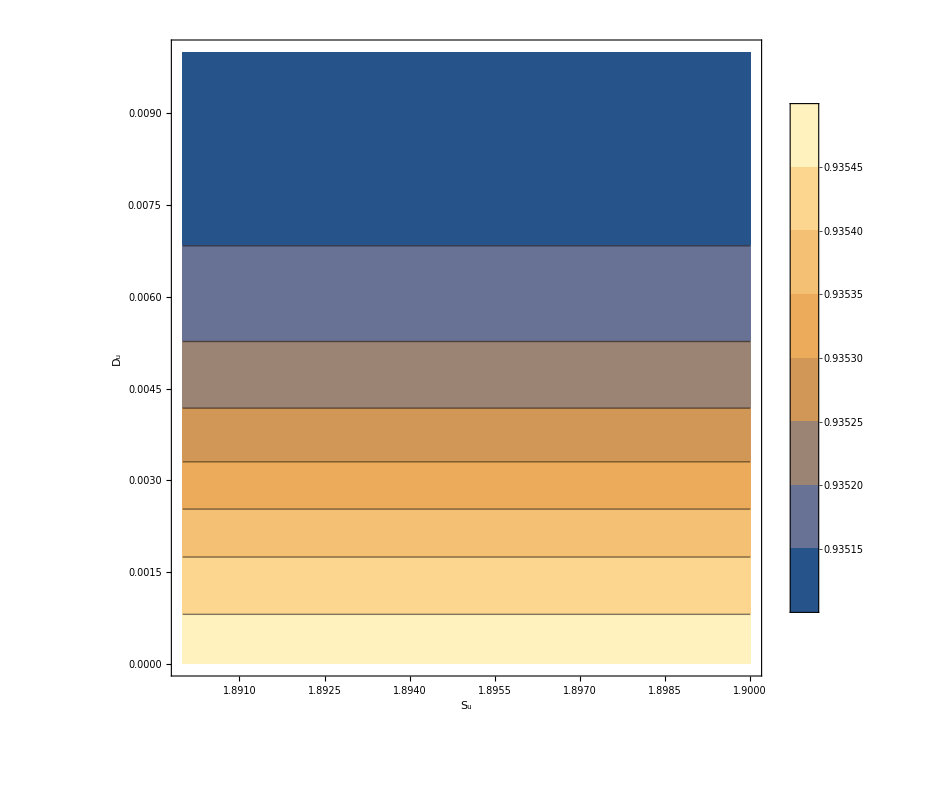

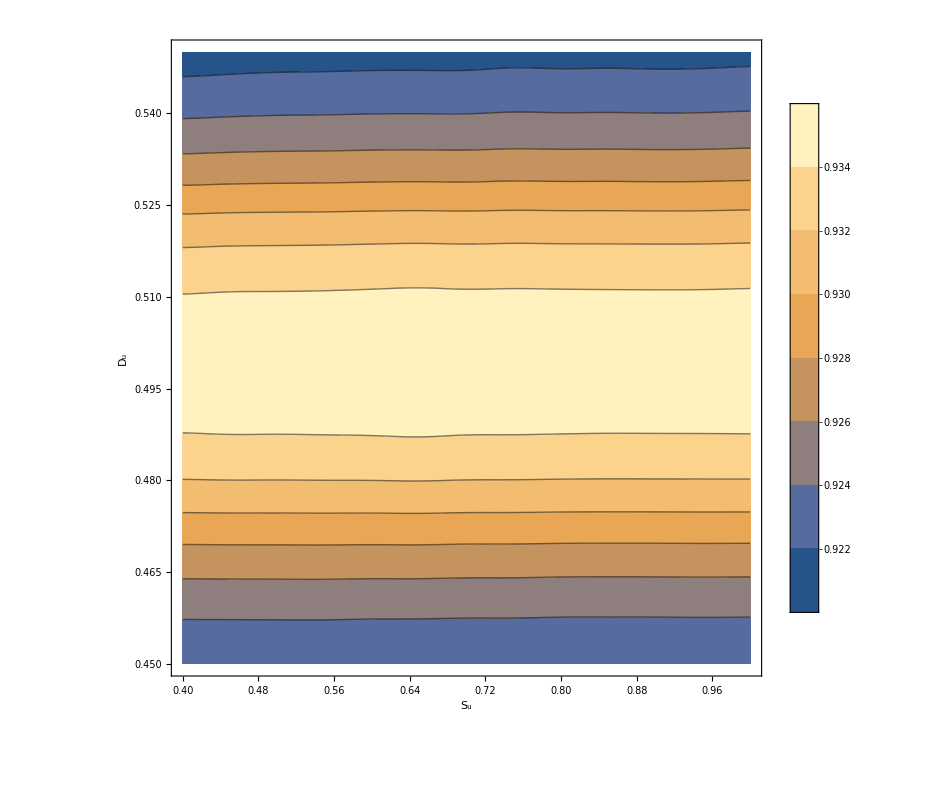

```mathematica
ListContourPlot[FMeasureSurface2,
DataRange->{{SuMin,SuMax},{DuMin,DuMax}},
InterpolationOrder->2,
ImageSize->800,
PlotLegends->Automatic,
ContourLabels->None,
Frame->True,
FrameLabel->{"S_u","D_u"},
LabelStyle->Directive[Bold, 20]]
```

```mathematica
0.935
```

```mathematica
Export["C:\\Users\\Byron\\Documents\\2017\\Research\\Nonlinear System for Image Binarization\\v1\\Ex2FMSurface.eps",%];
```

# Ex 3

```mathematica
pic="Bill";
imgfn=NotebookDirectory[]<>"\\Document Images\\"<>pic<>".png";
gtfn=NotebookDirectory[]<>"\\Document Images\\"<>pic<>"GT.png";


img=Image[ImageData[Import[imgfn]][[1;;-13,1;;-13]]];
img//ImageDimensions;
img;
count=0;
Du=2^0*0.217;
Dv=Du/4;
Su=2^0/dt 2.71;
Sv=4Su;
τ=0.45;

img=1-ImageData[ColorConvert[img,"Grayscale"]];
img=ImageData[ImageAdjust[Image[img]]];
averagingKernel[r1_,r2_]:=1/((2r1+1)(2r2+1))BoxMatrix[{r1,r2}];
Δimg=ImageData[ImageConvolve[Image[img],GaussianMatrix[{7,7}]]];
(*Δimg=ImageData[ImageConvolve[Image[img],averagingKernel[7,7]]];*)
(*v0=ImageData[ImageAdjust[Image[Δimg]]];*)
(*v0=ImageData[ImageAdjust[Image[img-Δimg]]];*)
(*v0=Δimg;*)
(*v0=ImageData[ImageAdjust[Image[img/Δimg]]];*)

u0=ImageData[ImageAdjust[Image[img-Δimg]]];
v0=ImageData[ImageConvolve[Image[u0],GaussianMatrix[{7,7}]]];
(*rad=15;
v0=ImageData[ImageConvolve[Image[u0],1/Apply[Times,Dimensions[BoxMatrix[rad]]] BoxMatrix[rad]]];
*)
AbsoluteTiming[test1=andGo[Du,Su,Dv,Sv,τ,u0,v0]]
```

{10.5992,592}

```mathematica
ArrayPlot[Abs[Round[gt]-Round[res]]]
ArrayPlot[Round[res]]
```

-Graphics-

-Graphics-

```mathematica
Image[1-res]
```

-Graphics-

```mathematica
Export["C:\\Users\\Byron\\Documents\\2017\\Research\\Nonlinear System for Image Binarization\\v1\\Ex3FN.eps",Image[1-res]];
```

## Compute Performance Scores

```mathematica
Module[{img=Round[res],gtt=Round[gt]},
tp=Table[img[[i,j]]==1&&img[[i,j]]==gtt[[i,j]],{i,1,n},{j,1,m}];

fp=Table[img[[i,j]]==1&&img[[i,j]]≠gtt[[i,j]],{i,1,n},{j,1,m}];
fn=Table[img[[i,j]]==0&&img[[i,j]]≠gtt[[i,j]],{i,1,n},{j,1,m}];
check=Image[fn/.{True->1,False->0}];
fn=Total[Total[fn/.{True->1,False->0}]];
tp=Total[Total[tp/.{True->1,False->0}]];
fp=Total[Total[fp/.{True->1,False->0}]];
precision=tp/(tp+fp);
recall=tp/(tp+fn);
]
precision//N
recall//N
(2.precision*recall)/(precision+recall)//N
1-Total[Total[Abs[Round[res]-Round[gt]]]]/(600*600.)
```

0.923499

0.845159

0.882594

0.976858

0.894489

0.908612

0.901496

0.979564

```mathematica
inc=0.005;
DuMin=0.2;
DuMax=0.22;
(*inc=0.05;
DuMin=0.2;
DuMax=0.45;*)
SuMin=2.65;
SuMax=2.85;
```

```mathematica
FMeasureSurface3Coords=Table[{Du,Su},{Du,DuMin,DuMax,inc},{Su,SuMin,SuMax,10*inc}];
FMeasureSurface3=Table[andGoFMSurface[Du,Su/dt,Du/4,(4 Su)/dt,0.4,"Bill"],{Du,DuMin,DuMax,inc},{Su,SuMin,SuMax,10*inc}];
(*FMeasureSurface3=Table[andGoFMSurface[2^0*0.01,Su/dt,(2^0*0.01)/4,(4 Su)/dt,Du,"Bill"],{Du,DuMin,DuMax,inc},{Su,SuMin,SuMax,inc}];*)
```

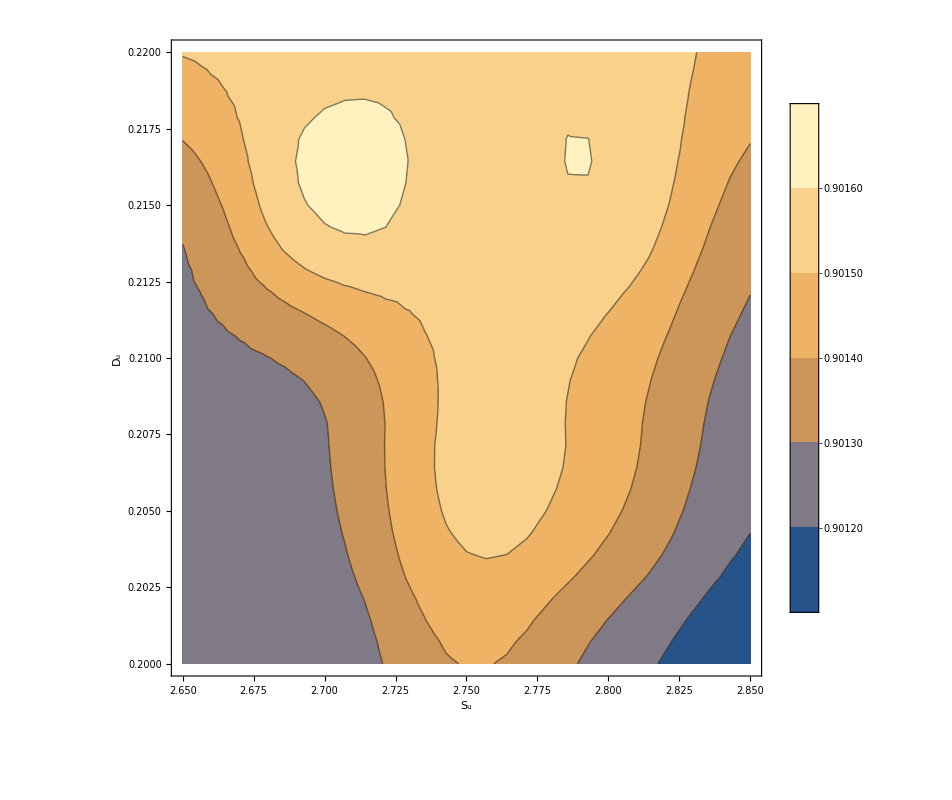

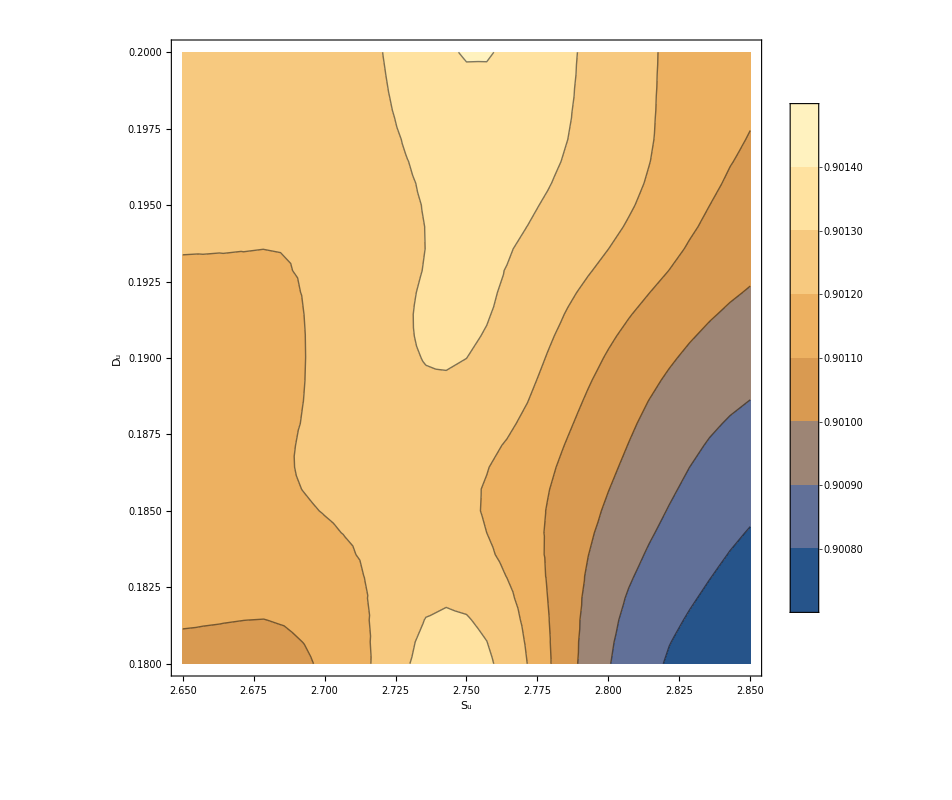

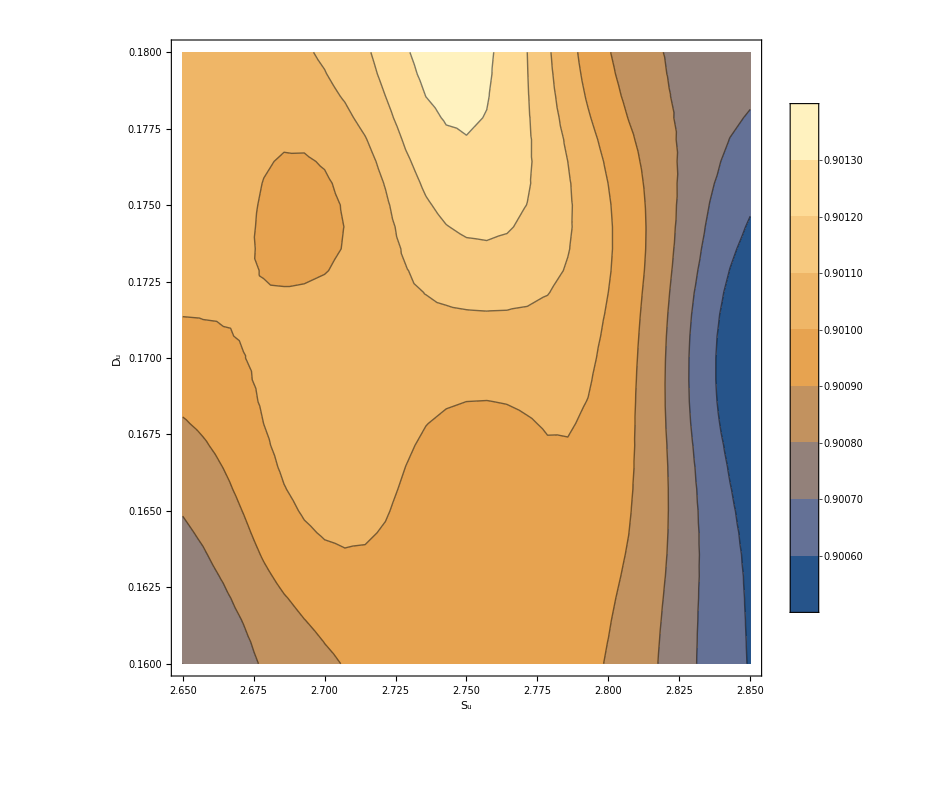

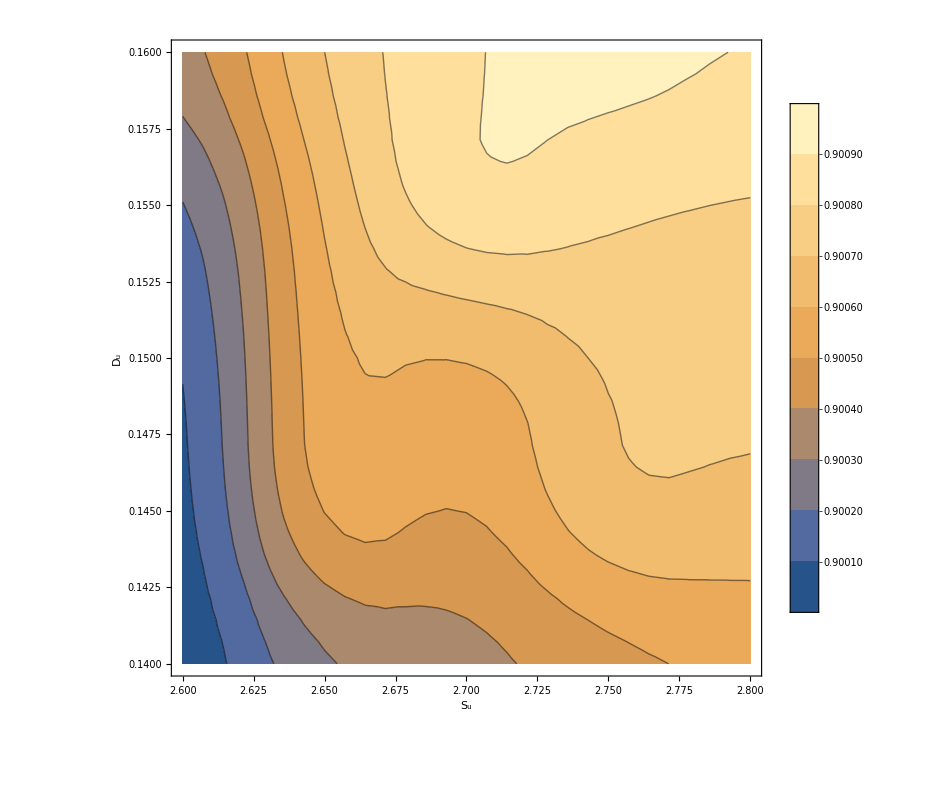

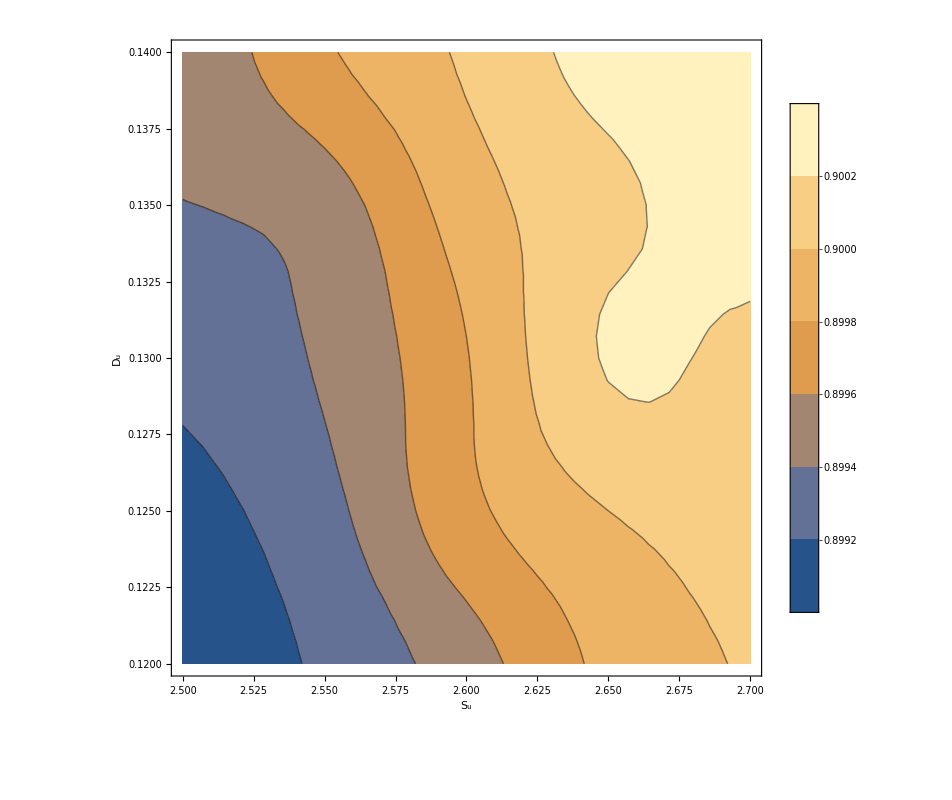

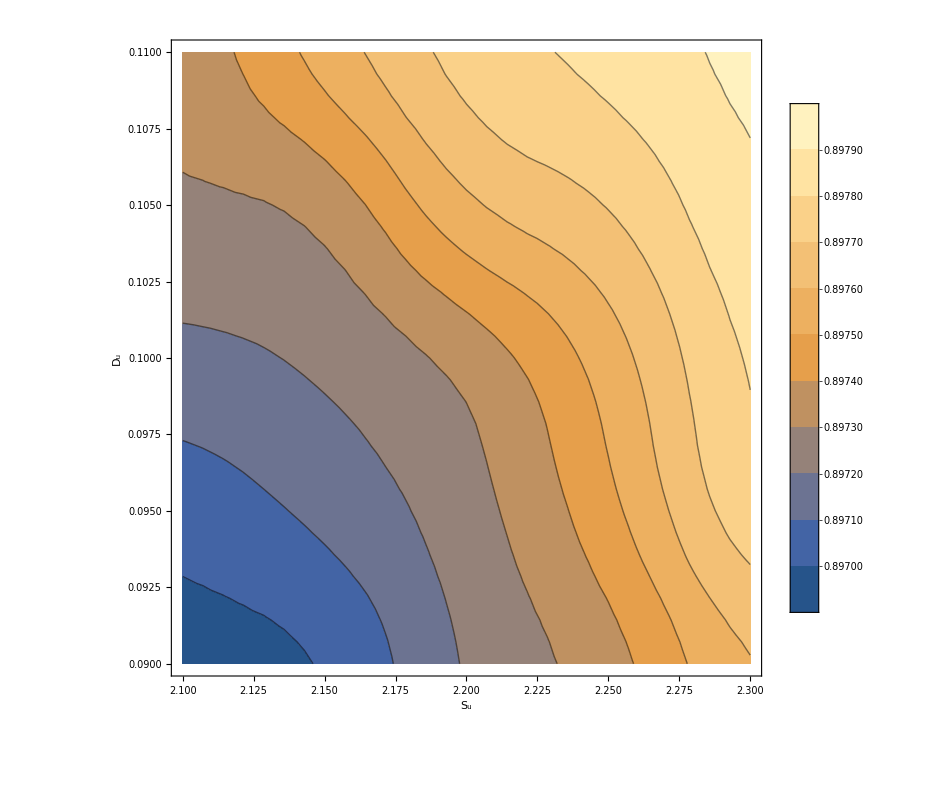

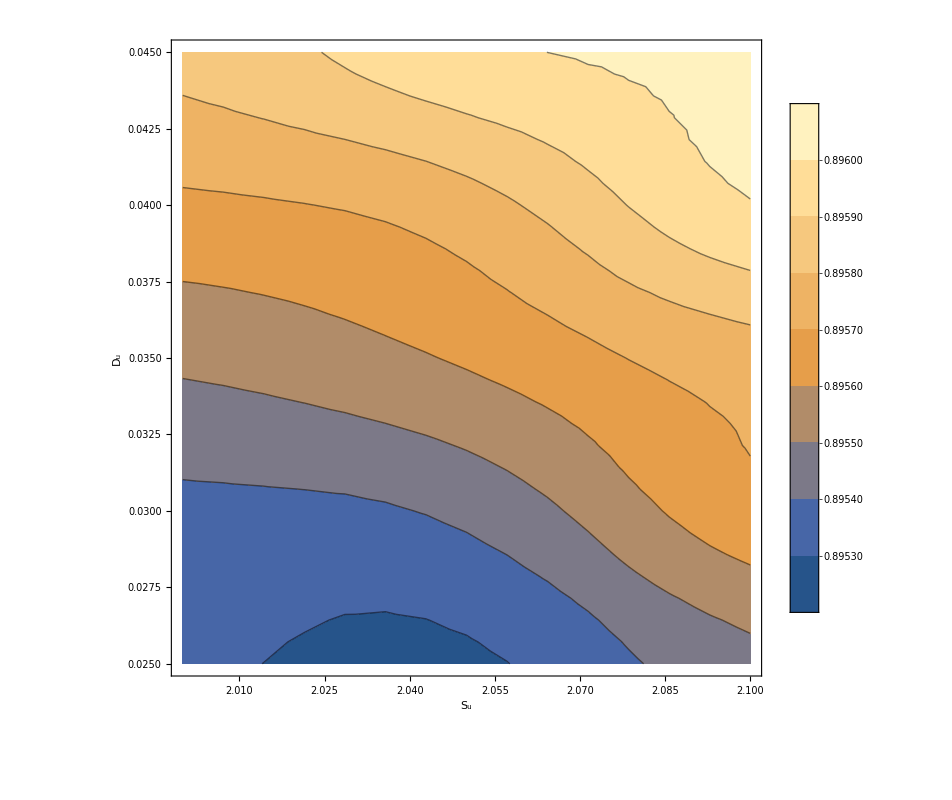

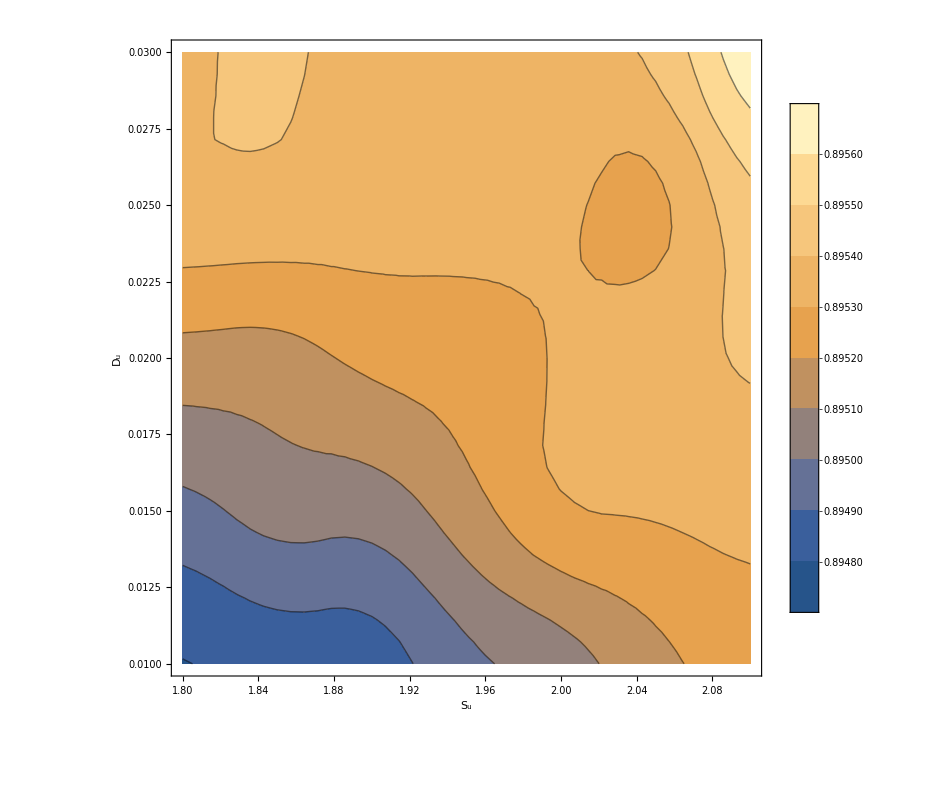

```mathematica
ListContourPlot[FMeasureSurface3,
DataRange->{{SuMin,SuMax},{DuMin,DuMax}},
InterpolationOrder->2,
ImageSize->800,
PlotLegends->Automatic,
ContourLabels->None,
Frame->True,
FrameLabel->{"S_u","D_u"},
LabelStyle->Directive[Bold, 20]]
```

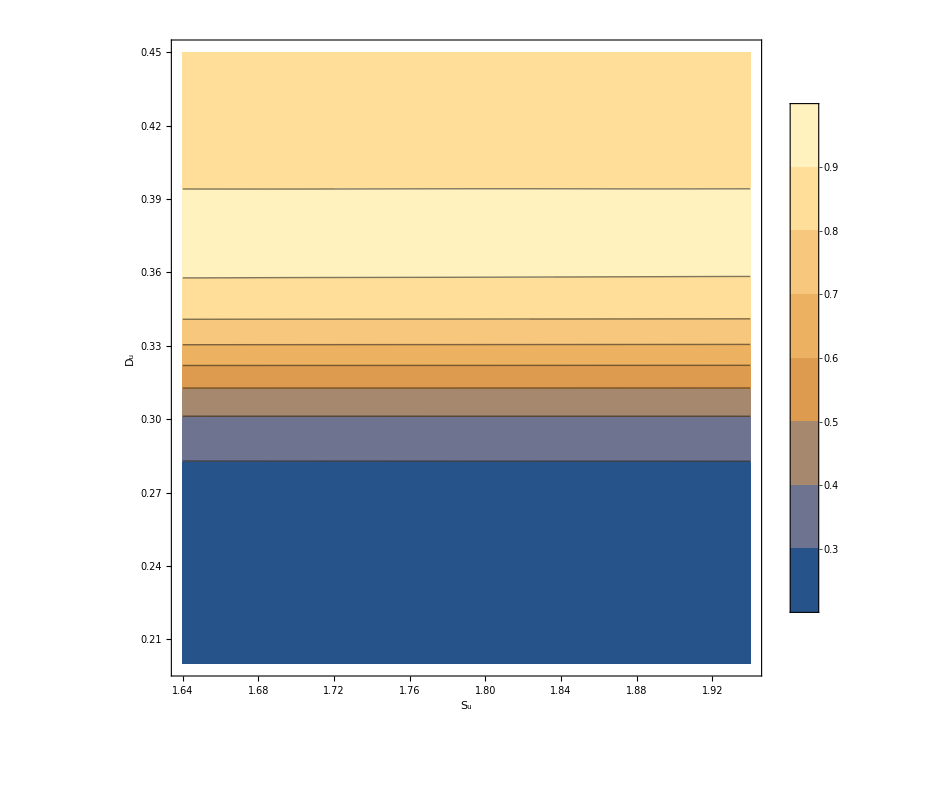

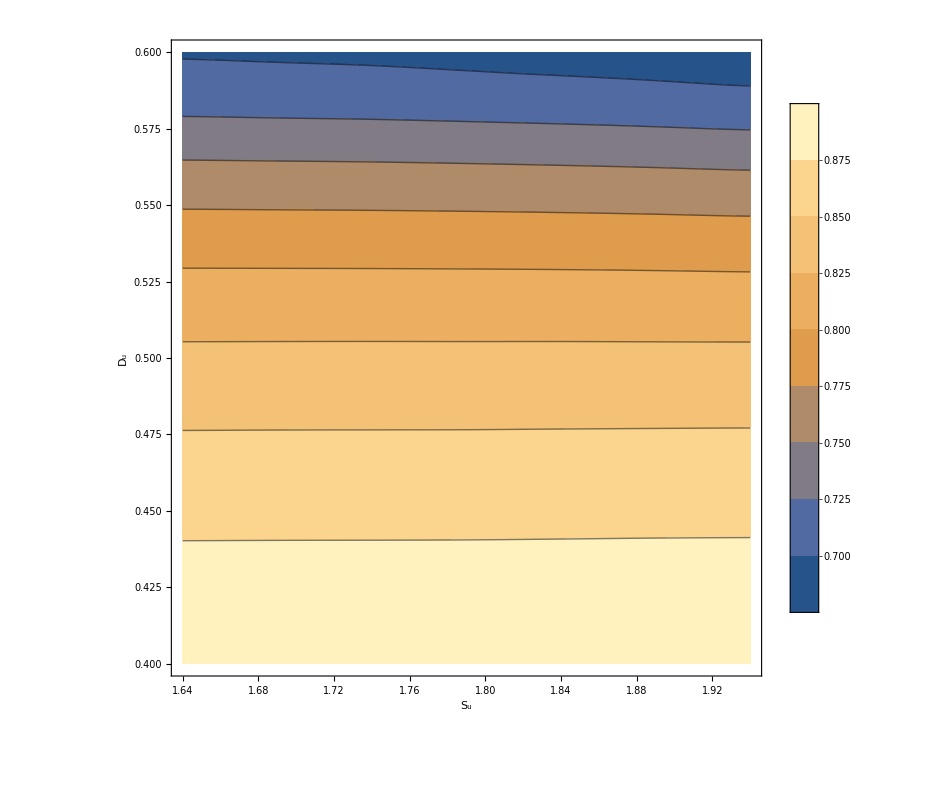

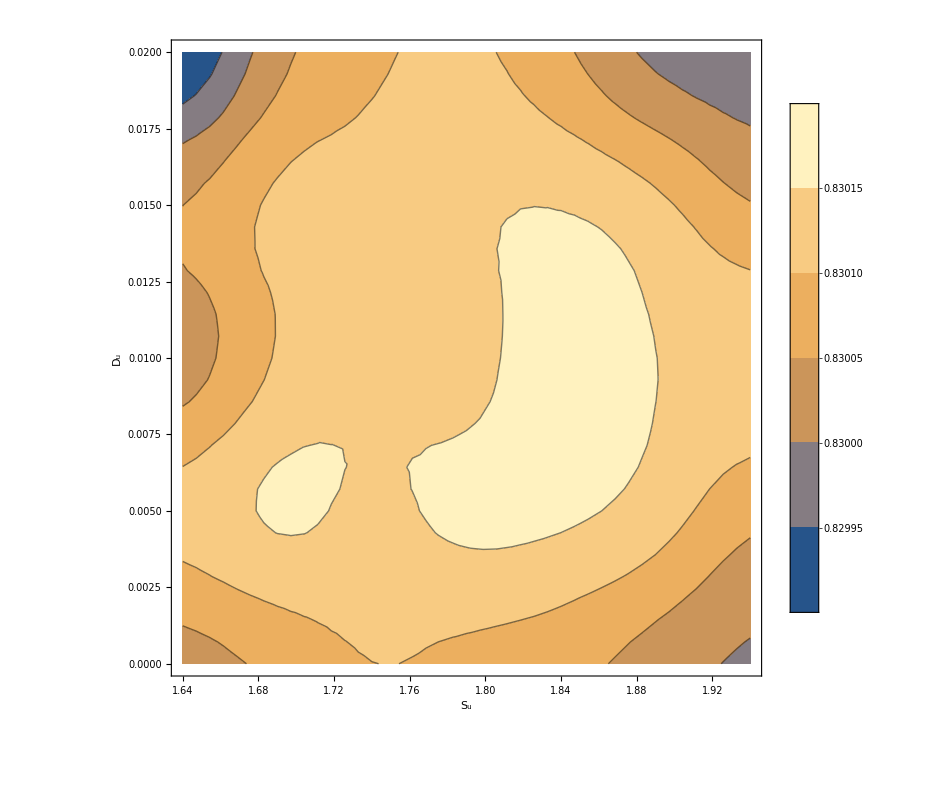

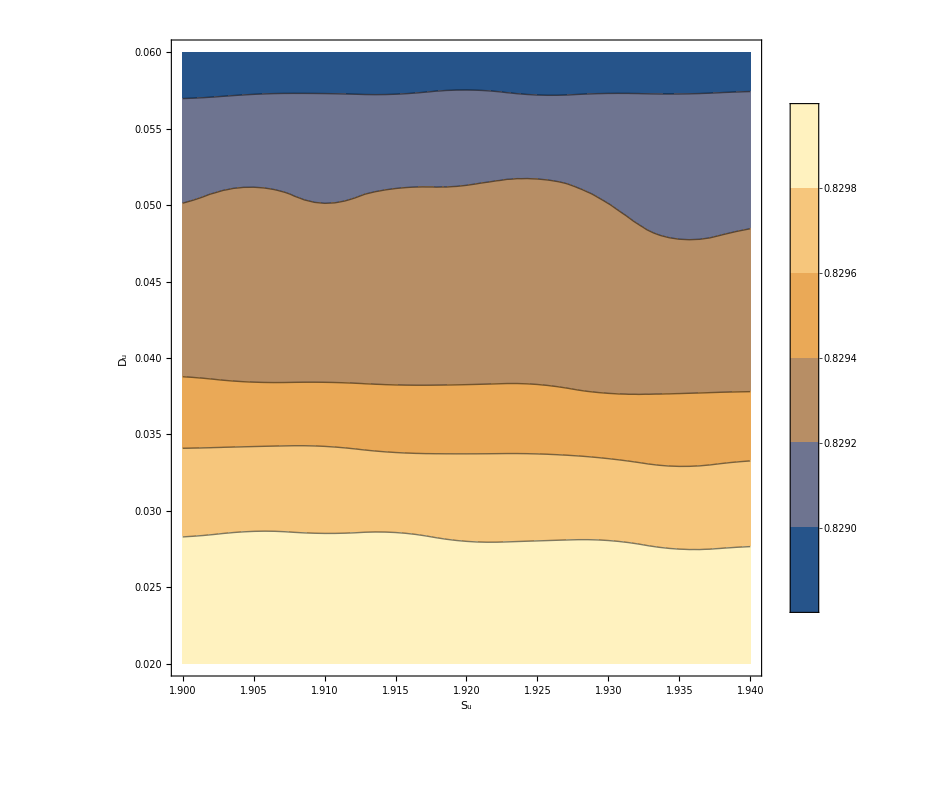

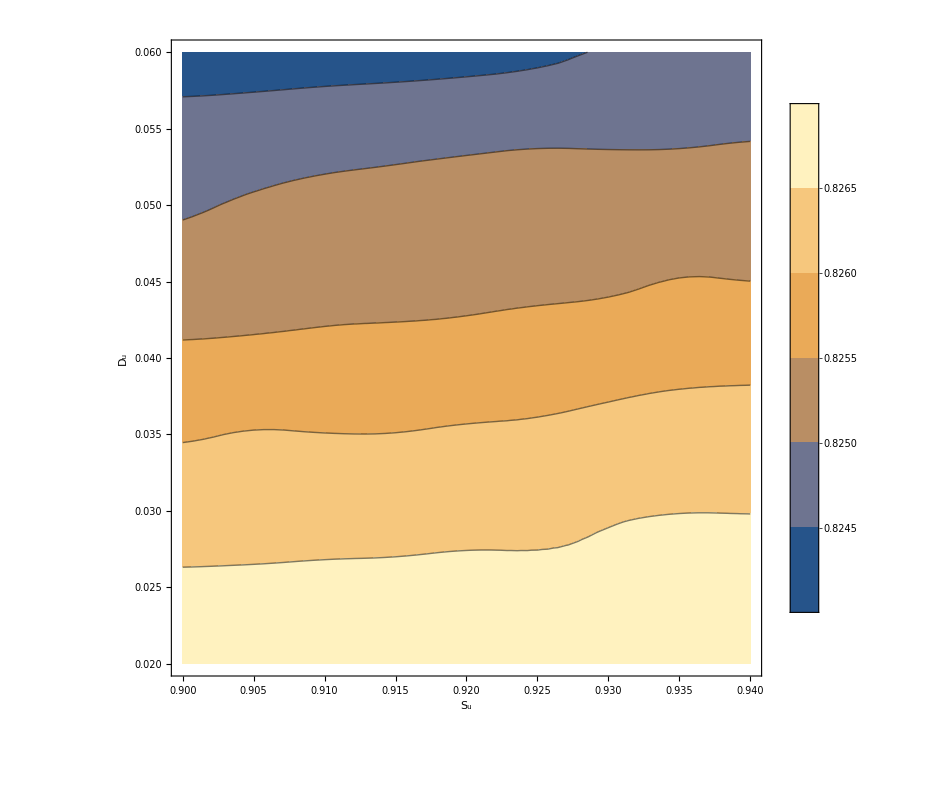

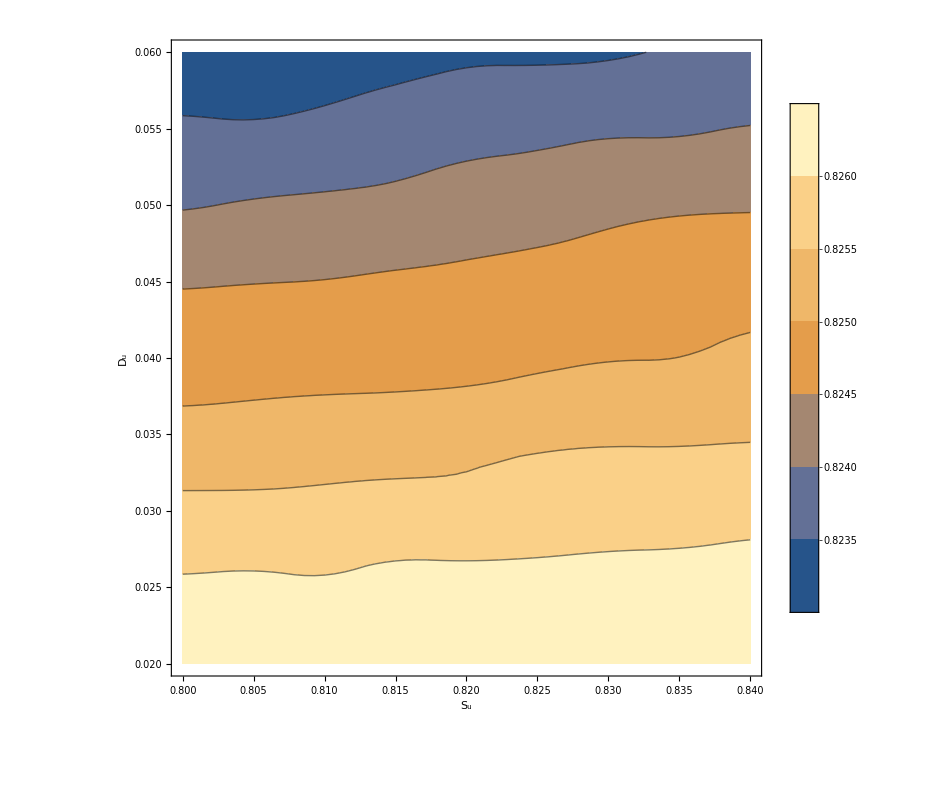

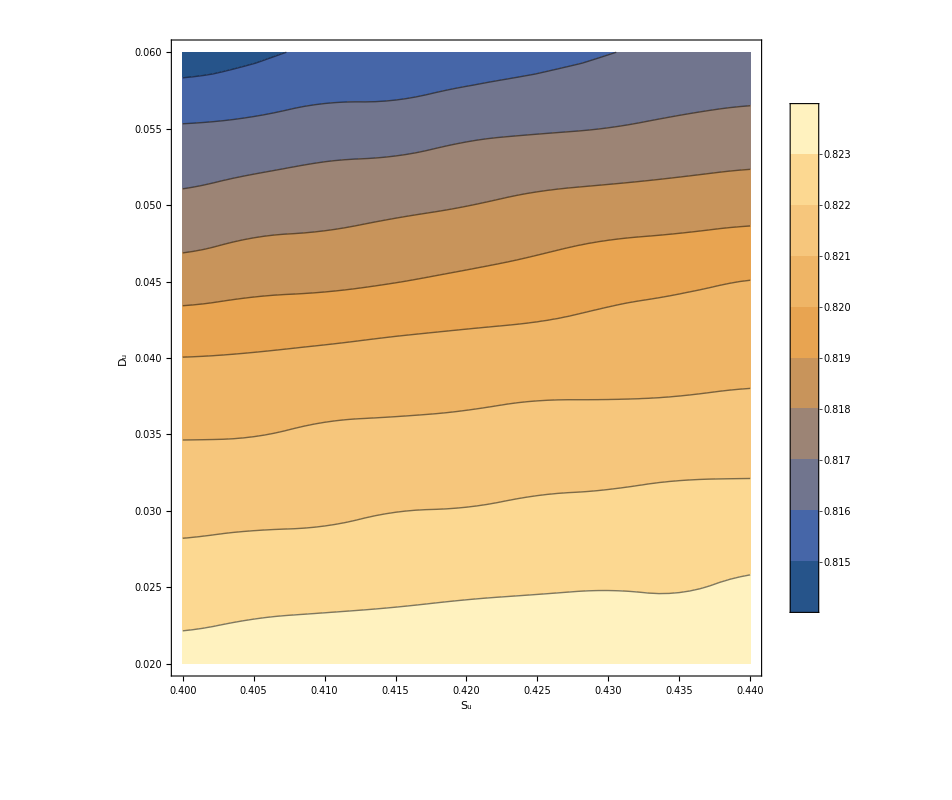

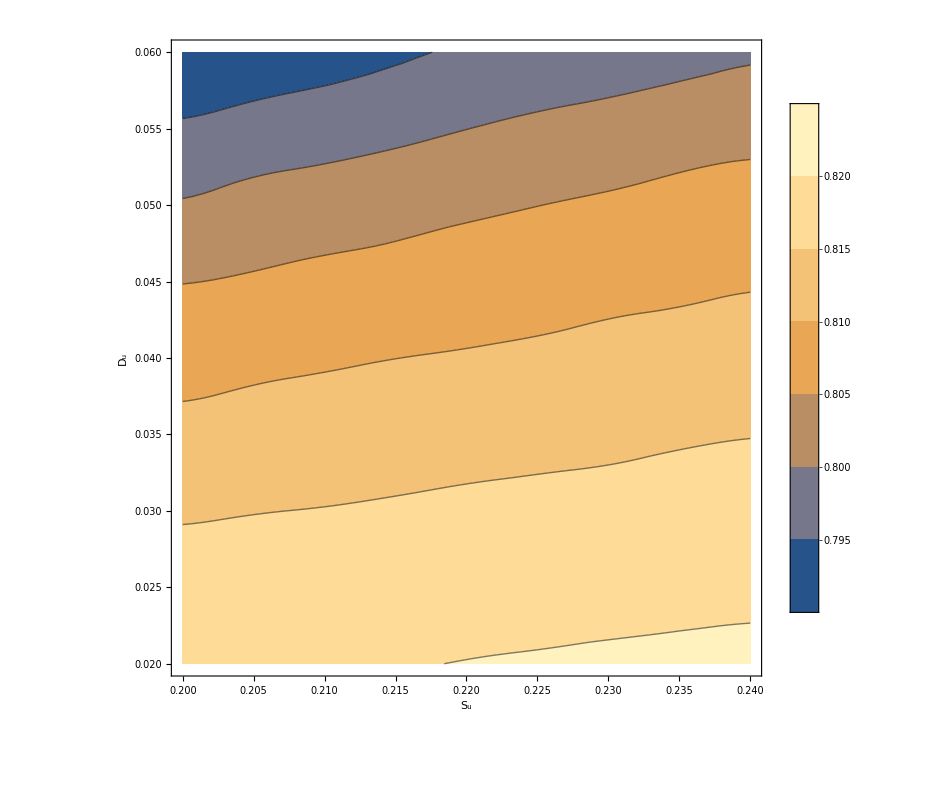

```mathematica
Export["C:\\Users\\Byron\\Documents\\2017\\Research\\Nonlinear System for Image Binarization\\v1\\Ex3FMSurface.eps",Out[900]];
```